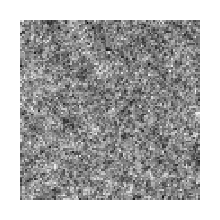

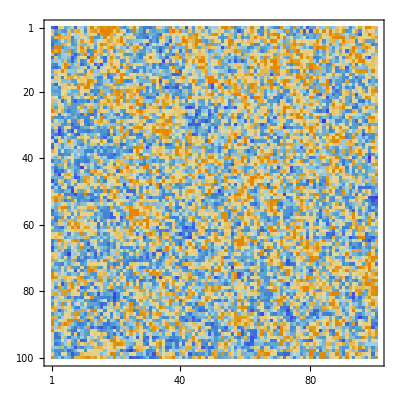

```mathematica
GaussNoise2D[2*Pi*Pi,(1/#)&,100];
Show[ap]
Show[mp]
```

```mathematica
ft=Fourier[RandomReal[
NormalDistribution[0,1],
200]
];
```

```mathematica
ft
InverseFourier[ft]
```

{-0.595028+0. ⅈ,0.0392851-0.598594 ⅈ,-0.342473+0.671095 ⅈ,0.666934+0.0190709 ⅈ,0.584665-0.670709 ⅈ,-0.802278+0. ⅈ,0.584665+0.670709 ⅈ,0.666934-0.0190709 ⅈ,-0.342473-0.671095 ⅈ,0.0392851+0.598594 ⅈ}

{0.157961,-0.467519,-0.200173,-0.331447,-1.06309,-0.227939,-0.332325,1.70866,-0.771705,-0.354067}

```mathematica
MapIndexed[(#1/#2[[1]])&,
Take[ft,Length[ft]/2]
]
```

{1.86545+0. ⅈ,-0.264461+0.355952 ⅈ,-0.114149-0.0629976 ⅈ,-0.1246+0.0690406 ⅈ,0.311755+0.338369 ⅈ,0.0739025+0.135097 ⅈ,-0.0639646+0.0350526 ⅈ,0.0055644+0.0128534 ⅈ,0.107333+0.0397793 ⅈ,-0.0984801+0.0930398 ⅈ,-0.0184486+0.0365581 ⅈ,-0.00910919-0.0104613 ⅈ,0.018611+0.00657555 ⅈ,0.00554799-0.102226 ⅈ,0.022731+0.0420743 ⅈ,0.131382-0.04719 ⅈ,-0.0151651-0.0240105 ⅈ,0.019705+0.0781916 ⅈ,0.0139693-0.0721733 ⅈ,-0.135202+0.0134197 ⅈ,-0.0123909-0.000542421 ⅈ,0.0278619-0.0108571 ⅈ,-0.0157893+0.0176019 ⅈ,-0.0406083+0.0540203 ⅈ,0.0627011+0.0280021 ⅈ,-0.0179218+0.00993121 ⅈ,-0.0638833-0.00022413 ⅈ,0.0317345+0.00317352 ⅈ,-0.0050348+0.0253961 ⅈ,-0.0125472-0.00657179 ⅈ,-0.0130635-0.0445638 ⅈ,-0.02357-0.00474565 ⅈ,0.0296723+0.0295497 ⅈ,-0.00993327+0.00969959 ⅈ,-0.0141643+0.0276092 ⅈ,-0.0284728-0.00929507 ⅈ,0.00117449-0.0233156 ⅈ,0.0102167+0.00925446 ⅈ,-0.0168673-0.0144359 ⅈ,0.013077-0.00150961 ⅈ,0.00027133-0.0158994 ⅈ,-0.0312325-0.0216732 ⅈ,0.00688556-0.0156172 ⅈ,-0.03935+0.00218103 ⅈ,-0.00512991+0.00519294 ⅈ,-0.0143365-0.00134483 ⅈ,-0.00284419+0.0275841 ⅈ,0.0159498-0.0412657 ⅈ,0.00147676-0.0198185 ⅈ,-0.0200896-0.0328986 ⅈ,-0.00214575+0.0143224 ⅈ,0.00120775-0.00426002 ⅈ,-0.00101259+0.010195 ⅈ,-0.02801+0.0107159 ⅈ,-0.0259526-0.00417972 ⅈ,-0.0121472+0.0203693 ⅈ,-0.0136644-0.0141641 ⅈ,0.00457678+0.0178219 ⅈ,-0.00382302-0.0166021 ⅈ,0.00999595-0.00603795 ⅈ,0.000966703+0.00951487 ⅈ,0.00113009-0.00478468 ⅈ,0.0029701-0.0176583 ⅈ,-0.0124638-0.00694957 ⅈ,0.015579-0.00780163 ⅈ,-0.00151426+0.00399381 ⅈ,0.00105244-0.00542339 ⅈ,0.00449013+0.00921462 ⅈ,-0.00576564+0.0187364 ⅈ,0.00839773+0.0221265 ⅈ,-0.00803179-0.00300528 ⅈ,0.018934+0.00588629 ⅈ,-0.0205051+0.00216176 ⅈ,0.0100322-0.00359844 ⅈ,-0.00375806-0.00579599 ⅈ,0.00121841+0.00283978 ⅈ,0.00676656-0.00522031 ⅈ,0.00831835+0.00161264 ⅈ,-0.0148907-0.0267245 ⅈ,-0.00438605-0.00221542 ⅈ,-0.00598714+0.00176477 ⅈ,-0.00300297+0.0114459 ⅈ,0.0013608-0.0130591 ⅈ,-0.0000455674+0.000586448 ⅈ,-0.00090207-0.00136901 ⅈ,0.0153468-0.00709115 ⅈ,-0.0095551-0.00544346 ⅈ,0.00539618-0.00992352 ⅈ,0.0078394+0.00347381 ⅈ,0.00200317-0.00615747 ⅈ,0.00554087-0.00157513 ⅈ,0.00338098-0.00186485 ⅈ,-0.0010376+0.0128512 ⅈ,0.0131983+0.00771494 ⅈ,0.0037767-0.00439863 ⅈ,0.014852-0.00439657 ⅈ,0.000987526-0.00662365 ⅈ,0.000398341+0.0140564 ⅈ,0.00359051+0.00274579 ⅈ,0.0128706+0.000165022 ⅈ}

```mathematica
Join[%,Drop[ft,Length[ft]/2]]
```

{1.86545+0. ⅈ,-0.264461+0.355952 ⅈ,-0.114149-0.0629976 ⅈ,-0.1246+0.0690406 ⅈ,0.311755+0.338369 ⅈ,0.0739025+0.135097 ⅈ,-0.0639646+0.0350526 ⅈ,0.0055644+0.0128534 ⅈ,0.107333+0.0397793 ⅈ,-0.0984801+0.0930398 ⅈ,-0.0184486+0.0365581 ⅈ,-0.00910919-0.0104613 ⅈ,0.018611+0.00657555 ⅈ,0.00554799-0.102226 ⅈ,0.022731+0.0420743 ⅈ,0.131382-0.04719 ⅈ,-0.0151651-0.0240105 ⅈ,0.019705+0.0781916 ⅈ,0.0139693-0.0721733 ⅈ,-0.135202+0.0134197 ⅈ,-0.0123909-0.000542421 ⅈ,0.0278619-0.0108571 ⅈ,-0.0157893+0.0176019 ⅈ,-0.0406083+0.0540203 ⅈ,0.0627011+0.0280021 ⅈ,-0.0179218+0.00993121 ⅈ,-0.0638833-0.00022413 ⅈ,0.0317345+0.00317352 ⅈ,-0.0050348+0.0253961 ⅈ,-0.0125472-0.00657179 ⅈ,-0.0130635-0.0445638 ⅈ,-0.02357-0.00474565 ⅈ,0.0296723+0.0295497 ⅈ,-0.00993327+0.00969959 ⅈ,-0.0141643+0.0276092 ⅈ,-0.0284728-0.00929507 ⅈ,0.00117449-0.0233156 ⅈ,0.0102167+0.00925446 ⅈ,-0.0168673-0.0144359 ⅈ,0.013077-0.00150961 ⅈ,0.00027133-0.0158994 ⅈ,-0.0312325-0.0216732 ⅈ,0.00688556-0.0156172 ⅈ,-0.03935+0.00218103 ⅈ,-0.00512991+0.00519294 ⅈ,-0.0143365-0.00134483 ⅈ,-0.00284419+0.0275841 ⅈ,0.0159498-0.0412657 ⅈ,0.00147676-0.0198185 ⅈ,-0.0200896-0.0328986 ⅈ,-0.00214575+0.0143224 ⅈ,0.00120775-0.00426002 ⅈ,-0.00101259+0.010195 ⅈ,-0.02801+0.0107159 ⅈ,-0.0259526-0.00417972 ⅈ,-0.0121472+0.0203693 ⅈ,-0.0136644-0.0141641 ⅈ,0.00457678+0.0178219 ⅈ,-0.00382302-0.0166021 ⅈ,0.00999595-0.00603795 ⅈ,0.000966703+0.00951487 ⅈ,0.00113009-0.00478468 ⅈ,0.0029701-0.0176583 ⅈ,-0.0124638-0.00694957 ⅈ,0.015579-0.00780163 ⅈ,-0.00151426+0.00399381 ⅈ,0.00105244-0.00542339 ⅈ,0.00449013+0.00921462 ⅈ,-0.00576564+0.0187364 ⅈ,0.00839773+0.0221265 ⅈ,-0.00803179-0.00300528 ⅈ,0.018934+0.00588629 ⅈ,-0.0205051+0.00216176 ⅈ,0.0100322-0.00359844 ⅈ,-0.00375806-0.00579599 ⅈ,0.00121841+0.00283978 ⅈ,0.00676656-0.00522031 ⅈ,0.00831835+0.00161264 ⅈ,-0.0148907-0.0267245 ⅈ,-0.00438605-0.00221542 ⅈ,-0.00598714+0.00176477 ⅈ,-0.00300297+0.0114459 ⅈ,0.0013608-0.0130591 ⅈ,-0.0000455674+0.000586448 ⅈ,-0.00090207-0.00136901 ⅈ,0.0153468-0.00709115 ⅈ,-0.0095551-0.00544346 ⅈ,0.00539618-0.00992352 ⅈ,0.0078394+0.00347381 ⅈ,0.00200317-0.00615747 ⅈ,0.00554087-0.00157513 ⅈ,0.00338098-0.00186485 ⅈ,-0.0010376+0.0128512 ⅈ,0.0131983+0.00771494 ⅈ,0.0037767-0.00439863 ⅈ,0.014852-0.00439657 ⅈ,0.000987526-0.00662365 ⅈ,0.000398341+0.0140564 ⅈ,0.00359051+0.00274579 ⅈ,0.0128706+0.000165022 ⅈ,-0.410072+0. ⅈ,1.28706-0.0165022 ⅈ,0.355461-0.271833 ⅈ,0.0390374-1.37752 ⅈ,0.09579+0.642494 ⅈ,1.4258+0.422071 ⅈ,0.358786+0.41787 ⅈ,1.24064-0.725204 ⅈ,-0.0964967-1.19516 ⅈ,0.31105+0.171566 ⅈ,0.504219+0.143337 ⅈ,0.180286+0.554172 ⅈ,0.697707-0.309169 ⅈ,0.474864+0.87327 ⅈ,-0.831293+0.473581 ⅈ,1.31982+0.609839 ⅈ,-0.076676+0.116366 ⅈ,-0.00382767-0.0492616 ⅈ,0.112946+1.08391 ⅈ,-0.246244-0.938562 ⅈ,-0.484958-0.142947 ⅈ,-0.350884+0.177234 ⅈ,-1.17637+2.11123 ⅈ,0.648832-0.125786 ⅈ,0.521025+0.401964 ⅈ,0.0925995-0.215823 ⅈ,-0.281854+0.434699 ⅈ,0.74238+0.266285 ⅈ,-1.49687-0.157809 ⅈ,1.36325-0.423813 ⅈ,-0.570257+0.213375 ⅈ,0.587841-1.54885 ⅈ,-0.397829-1.29281 ⅈ,0.305329-0.626594 ⅈ,0.0705133+0.363367 ⅈ,-0.0999412-0.263591 ⅈ,1.01264+0.507106 ⅈ,-0.797686+0.444772 ⅈ,0.187116+1.11248 ⅈ,0.0700656+0.29665 ⅈ,0.0589689-0.580407 ⅈ,0.599757+0.362277 ⅈ,-0.225558+0.979521 ⅈ,0.265453-1.03367 ⅈ,-0.778873+0.807355 ⅈ,-0.680245-1.14068 ⅈ,-1.42739+0.229885 ⅈ,-1.51254-0.578656 ⅈ,-0.0536674-0.540337 ⅈ,0.0628028+0.221521 ⅈ,-0.109433-0.730442 ⅈ,-1.00448+1.64493 ⅈ,0.0723615+0.971106 ⅈ,0.765591+1.98076 ⅈ,-0.133677-1.29645 ⅈ,-0.659479+0.0618621 ⅈ,-0.230846-0.233682 ⅈ,-1.7314-0.0959654 ⅈ,0.296079+0.671537 ⅈ,-1.31176+0.910274 ⅈ,0.0111245+0.651873 ⅈ,0.523081+0.0603844 ⅈ,-0.657823+0.563002 ⅈ,0.388236-0.35167 ⅈ,0.043456+0.862676 ⅈ,-1.02502+0.334623 ⅈ,-0.495749-0.96632 ⅈ,-0.337731-0.329786 ⅈ,0.979187-0.975139 ⅈ,-0.75424+0.151861 ⅈ,-0.40497+1.38148 ⅈ,-0.376417+0.197154 ⅈ,-0.146009-0.736486 ⅈ,0.888567-0.0888585 ⅈ,-1.72485+0.00605151 ⅈ,-0.465966-0.258212 ⅈ,1.56753-0.700052 ⅈ,-0.9746-1.29649 ⅈ,-0.363153-0.404843 ⅈ,0.612962+0.238857 ⅈ,-0.260208+0.0113908 ⅈ,-2.70404-0.268393 ⅈ,0.265416+1.37129 ⅈ,0.354689-1.40745 ⅈ,-0.257807+0.408179 ⅈ,2.10211+0.75504 ⅈ,0.340965-0.631115 ⅈ,0.0776718+1.43117 ⅈ,0.241943-0.0854821 ⅈ,-0.10931+0.125535 ⅈ,-0.202935-0.402139 ⅈ,-0.984801-0.930398 ⅈ,0.965996-0.358014 ⅈ,0.0445152-0.102827 ⅈ,-0.447752-0.245368 ⅈ,0.443415-0.810584 ⅈ,1.55878-1.69185 ⅈ,-0.4984-0.276162 ⅈ,-0.342448+0.188993 ⅈ,-0.528922-0.711903 ⅈ}

```mathematica
InverseFourier[%]
```

{-0.152333+0.0287574 ⅈ,-0.666911-0.945729 ⅈ,1.41467-0.875883 ⅈ,0.443151+0.421122 ⅈ,0.777563+0.00556142 ⅈ,-0.386425+0.634083 ⅈ,0.306214-0.838744 ⅈ,0.294099+0.622189 ⅈ,-0.219298-0.867299 ⅈ,1.18989-0.0114343 ⅈ,0.0672171+0.327999 ⅈ,0.209073-0.300744 ⅈ,0.881108-0.308339 ⅈ,0.830476+0.789249 ⅈ,-0.309329+0.364532 ⅈ,0.382243-0.181716 ⅈ,0.478963+0.539985 ⅈ,-0.266662+0.496602 ⅈ,-0.0824394-0.00655821 ⅈ,-0.075864+0.246963 ⅈ,0.0459647-0.0117415 ⅈ,-0.0942696+0.729223 ⅈ,-1.17019+0.0761135 ⅈ,-0.574392-0.936116 ⅈ,0.521963-0.883625 ⅈ,0.541747+0.11589 ⅈ,0.0618211-0.457598 ⅈ,1.1002-0.147684 ⅈ,0.479069+0.713052 ⅈ,-0.116311+0.522902 ⅈ,-0.317681+0.00935972 ⅈ,0.229843+0.00530853 ⅈ,-0.0809125+0.372705 ⅈ,-0.290354+0.276702 ⅈ,-0.740757+0.0109495 ⅈ,-0.34638-0.631116 ⅈ,0.0155358-0.528953 ⅈ,0.537301-0.57554 ⅈ,0.609212+0.287514 ⅈ,-0.0617535+0.179588 ⅈ,-0.0276438+0.149983 ⅈ,-0.50648-0.123148 ⅈ,-0.0751497-0.696232 ⅈ,0.426546-0.551315 ⅈ,0.590296-0.170498 ⅈ,0.343386-0.0210316 ⅈ,0.158699+0.00998684 ⅈ,0.0409654-0.544041 ⅈ,0.801321-0.261897 ⅈ,0.0519821-0.307164 ⅈ,1.40811-0.772547 ⅈ,0.950598+0.912258 ⅈ,0.103374+0.0352885 ⅈ,0.461113+0.138198 ⅈ,0.35934-0.0770522 ⅈ,0.359642+0.139113 ⅈ,0.420964-0.393729 ⅈ,0.985056+0.132353 ⅈ,0.61556+0.320406 ⅈ,0.543523+0.531979 ⅈ,0.219829+0.510863 ⅈ,-0.098752+0.578399 ⅈ,-0.225675+0.0700696 ⅈ,-0.176439+0.315843 ⅈ,-0.594354-0.412285 ⅈ,0.473691-0.734118 ⅈ,0.836558+0.0281375 ⅈ,0.419835+0.362432 ⅈ,0.425983+0.545584 ⅈ,-0.874456+0.816823 ⅈ,-0.536092-1.19742 ⅈ,0.917594+0.0490384 ⅈ,-0.31884-0.0943809 ⅈ,0.647711-0.25903 ⅈ,0.00769406+0.109956 ⅈ,0.479725-0.37769 ⅈ,0.581655+0.134584 ⅈ,0.530881+0.267139 ⅈ,0.15488+0.655832 ⅈ,-0.601198+0.248449 ⅈ,-0.0970007-0.711478 ⅈ,0.865651-0.107176 ⅈ,0.333756+0.743811 ⅈ,-0.808335+0.27117 ⅈ,0.296909-0.909782 ⅈ,0.509586+0.976686 ⅈ,-1.24586-0.387412 ⅈ,0.723066-0.902464 ⅈ,0.472692+0.0178514 ⅈ,0.635777+0.159076 ⅈ,-0.135464+0.341785 ⅈ,0.110879-0.203276 ⅈ,0.143189-0.0356425 ⅈ,0.320178+0.00141096 ⅈ,-0.0938201+0.202848 ⅈ,-0.212103-0.465761 ⅈ,0.841887-0.566859 ⅈ,0.367306+0.828833 ⅈ,-0.611809-0.792261 ⅈ,1.47383-0.295716 ⅈ,-0.0956186+0.463492 ⅈ,0.862629-0.445248 ⅈ,0.334047+0.883351 ⅈ,-0.321342-0.123695 ⅈ,0.260671-0.438577 ⅈ,0.867961-0.0624402 ⅈ,0.265654+0.327837 ⅈ,0.544854+0.134375 ⅈ,-0.285384+0.263457 ⅈ,0.995095-0.82447 ⅈ,1.08275+1.59436 ⅈ,-1.12692+0.637849 ⅈ,-0.167622-0.283922 ⅈ,0.0409576+0.0318721 ⅈ,-0.0721771+0.334151 ⅈ,-0.629097-0.0215785 ⅈ,-0.370837-0.4909 ⅈ,-0.0301048-1.02022 ⅈ,1.2319-0.789068 ⅈ,1.17816+0.217175 ⅈ,0.914775+0.590361 ⅈ,0.138591+0.771414 ⅈ,0.139307+0.319115 ⅈ,-0.157978+0.435393 ⅈ,0.366201-0.0492683 ⅈ,0.0661468+1.20257 ⅈ,-0.96263+0.148196 ⅈ,-0.227339+0.242863 ⅈ,-0.891579-0.0599758 ⅈ,-0.337551-0.245017 ⅈ,-0.677822-0.702612 ⅈ,0.746189-0.953331 ⅈ,0.760665+0.122551 ⅈ,0.589807+0.259812 ⅈ,0.347752+0.627705 ⅈ,-0.138854+0.88248 ⅈ,-0.86823+0.458597 ⅈ,-0.658031+0.0760289 ⅈ,-0.87896-0.092763 ⅈ,-0.749791-0.480664 ⅈ,-0.374476-1.07595 ⅈ,0.642918-0.551885 ⅈ,0.0361886-0.303301 ⅈ,0.689456-0.463269 ⅈ,0.450939-0.035643 ⅈ,0.911172+0.196182 ⅈ,-0.287012+1.01639 ⅈ,-0.849542-0.421616 ⅈ,0.237608-0.721243 ⅈ,0.336667-0.146123 ⅈ,0.389872-0.626505 ⅈ,1.09881+0.384273 ⅈ,-0.378001+0.140795 ⅈ,1.03747-0.194393 ⅈ,-0.25792+0.956979 ⅈ,-0.243754-0.340273 ⅈ,-0.328455-0.210941 ⅈ,0.830552-0.953963 ⅈ,0.677864+0.750826 ⅈ,-0.0899581-0.150147 ⅈ,0.266959-0.00828548 ⅈ,0.591621-0.227667 ⅈ,0.134557+0.639739 ⅈ,-0.0119972-0.566493 ⅈ,0.551122+0.187612 ⅈ,0.527836-0.55967 ⅈ,1.30481+1.12572 ⅈ,-0.997318+0.722822 ⅈ,0.0661974-0.417988 ⅈ,0.148088+0.113603 ⅈ,0.249021+0.098753 ⅈ,0.0895925+0.267562 ⅈ,-0.188839+0.303504 ⅈ,-0.199336-0.490556 ⅈ,0.937746+0.101557 ⅈ,-0.137425+0.736153 ⅈ,-0.0543562+0.156395 ⅈ,-0.405916+0.393366 ⅈ,-0.0949714-0.32146 ⅈ,0.247983+0.570436 ⅈ,-0.740308+0.447318 ⅈ,-0.782656-0.00926744 ⅈ,-0.837479-0.915798 ⅈ,1.07297-0.964995 ⅈ,0.490188+0.952429 ⅈ,-0.539047-0.181297 ⅈ,0.603712-0.101311 ⅈ,0.112835+0.740466 ⅈ,-0.669574+0.377251 ⅈ,-0.232326-0.151813 ⅈ,-0.41078+0.451229 ⅈ,-0.725658-0.278027 ⅈ,-0.451374-0.0532546 ⅈ,-0.598171-0.872919 ⅈ,0.634337-0.444427 ⅈ,0.0105912+0.185294 ⅈ,-0.357501-0.0473838 ⅈ,-0.117145-0.866421 ⅈ,0.860806-0.00438906 ⅈ,-0.220768+0.218454 ⅈ}

```mathematica
pink=%;
```

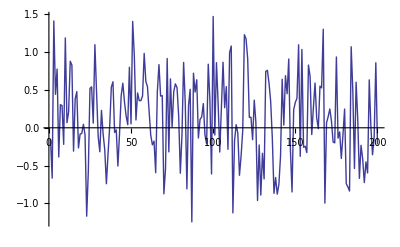

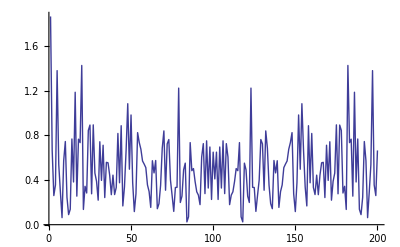

```mathematica
ListLinePlot[Re[pink],PlotRange->All]
ListLinePlot[Abs[Fourier[Re[pink]]],PlotRange->All]
```

```mathematica
ft
```

{-0.212068+0. ⅈ,-1.60898-0.509998 ⅈ,0.191526-0.88713 ⅈ,0.505688-0.588043 ⅈ,1.50081-0.0168529 ⅈ,-0.925576+0. ⅈ,1.50081+0.0168529 ⅈ,0.505688+0.588043 ⅈ,0.191526+0.88713 ⅈ,-1.60898+0.509998 ⅈ}

```mathematica
List
```

```mathematica
{ft[[5]],ft[[Length[ft]-6]]}
```

{0.506274-0.00161347 ⅈ,0.622682+0.0256314 ⅈ}

```mathematica
ft1=Take[ft,Length[ft]/2];
ftman=Table[
ft1[[i]]*1/Sqrt[i],{i,2,Length[ft1]}];
```

```mathematica
Take[ft,Length[ft]/2]
Drop[ft,Length[ft]/2]
```

{2.55904+0. ⅈ,0.106673-0.389159 ⅈ,0.896444-0.159248 ⅈ,0.102237-0.0403576 ⅈ,-0.0309052-1.24054 ⅈ}

{-1.05323+0. ⅈ,-0.0309052+1.24054 ⅈ,0.102237+0.0403576 ⅈ,0.896444+0.159248 ⅈ,0.106673+0.389159 ⅈ}

```mathematica
Join[ftman,Drop[ft,Length[ft]/2]]
```

{-1.60898-0.509998 ⅈ,0.135429-0.627296 ⅈ,0.291959-0.339507 ⅈ,0.750403-0.00842645 ⅈ,-0.925576+0. ⅈ,1.50081+0.0168529 ⅈ,0.505688+0.588043 ⅈ,0.191526+0.88713 ⅈ,-1.60898+0.509998 ⅈ}

```mathematica
InverseFourier[Join[ftman,Drop[ft,Length[ft]/2]]]
```

{-0.146553+0.275886 ⅈ,-1.89306-0.348181 ⅈ,-0.949094-1.44214 ⅈ,0.133875+0.193742 ⅈ,0.0108699-1.09103 ⅈ,0.0705819+0.963334 ⅈ,0.0518245-0.249745 ⅈ,-0.359753+0.645016 ⅈ,-0.331857-0.0287494 ⅈ}

```mathematica
3
```

```mathematica
Fourier[{{1,2},{3,4}}]//MatrixForm
Fourier[{1,2}]
Fourier[{3,4}]
Fourier[{1,3}]
Fourier[{2,4}]
```

(5. | -1.
-2. | 0.)

{2.12132+0. ⅈ,-0.707107+0. ⅈ}

{4.94975+0. ⅈ,-0.707107+0. ⅈ}

{2.82843+0. ⅈ,-1.41421+0. ⅈ}

{4.24264+0. ⅈ,-1.41421+0. ⅈ}

```mathematica
Chop[Append[{Fourier[{1,2}]},
Fourier[{3,4}]
]]//MatrixForm
```

(2.12132 | -0.707107
4.94975 | -0.707107)

```mathematica
Chop[
Append[
{Fourier[{2.121320343559643,4.949747468305833}]},
Fourier[{-0.7071067811865476,-0.7071067811865476}]
]
]//MatrixForm
```

(5. | -2.
-1. | 0)

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
Chop[
Fourier[A]
]//MatrixForm
```

(15. | -1.5-0.866025 ⅈ | -1.5+0.866025 ⅈ
-4.5-2.59808 ⅈ | 0 | 0
-4.5+2.59808 ⅈ | 0 | 0)

```mathematica
Map[Fourier[#]&,A]
```

{{3.4641+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ},{8.66025+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ},{13.8564+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}}

```mathematica
Map[Fourier[#]&,Transpose[%]]
```

{{15.+0. ⅈ,-4.5-2.59808 ⅈ,-4.5+2.59808 ⅈ},{-1.5-0.866025 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.5+0.866025 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Transpose[%]
```

{{15.+0. ⅈ,-1.5-0.866025 ⅈ,-1.5+0.866025 ⅈ},{-4.5-2.59808 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-4.5+2.59808 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Map[Fourier[#]&,A]
```

{{3.4641+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ},{8.66025+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ},{13.8564+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}}

```mathematica
Map[Fourier[#]&,Transpose[%]]
```

{{15.+0. ⅈ,-4.5-2.59808 ⅈ,-4.5+2.59808 ⅈ},{-1.5-0.866025 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.5+0.866025 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
MatrixForm[Chop[%]]
```

(15. | -4.5-2.59808 ⅈ | -4.5+2.59808 ⅈ
-1.5-0.866025 ⅈ | 0 | 0
-1.5+0.866025 ⅈ | 0 | 0)

```mathematica
B=Table[
{RandomReal[],RandomReal[],RandomReal[]},{3}]
B//MatrixForm
Fourier[B]//MatrixForm
Transpose[
Map[Fourier[#]&,
Transpose[
Map[
Fourier[#]&,B
]
]
]
]//MatrixForm
```

{{0.988513,0.0709915,0.425626},{0.875177,0.52869,0.201653},{0.592222,0.764064,0.744978}}

(0.988513 | 0.0709915 | 0.425626
0.875177 | 0.52869 | 0.201653
0.592222 | 0.764064 | 0.744978)

(1.73064+0. ⅈ | 0.362637-0.002457 ⅈ | 0.362637+0.002457 ⅈ
-0.122754-0.143109 ⅈ | 0.111796+0.0417451 ⅈ | 0.265772+0.34641 ⅈ
-0.122754+0.143109 ⅈ | 0.265772-0.34641 ⅈ | 0.111796-0.0417451 ⅈ)

(1.73064+0. ⅈ | 0.362637-0.002457 ⅈ | 0.362637+0.002457 ⅈ
-0.122754-0.143109 ⅈ | 0.111796+0.0417451 ⅈ | 0.265772+0.34641 ⅈ
-0.122754+0.143109 ⅈ | 0.265772-0.34641 ⅈ | 0.111796-0.0417451 ⅈ)

```mathematica
B=Table[
{RandomReal[],RandomReal[],RandomReal[],RandomReal[]},{4}];
B//MatrixForm
fB=Chop[Fourier[B]];
fB//MatrixForm
```

(0.0444375 | 0.220384 | 0.0612134 | 0.80886
0.343913 | 0.803528 | 0.421911 | 0.352535
0.438769 | 0.284401 | 0.985443 | 0.946659
0.437197 | 0.0381178 | 0.937265 | 0.321709)

(1.86159 | -0.285379-0.270833 ⅈ | -0.0265112 | -0.285379+0.270833 ⅈ
-0.380094+0.0468996 ⅈ | -0.0511712+0.123963 ⅈ | -0.279186-0.351219 ⅈ | 0.316121+0.0870722 ⅈ
0.0334978 | 0.00365375-0.354534 ⅈ | -0.33871 | 0.00365375+0.354534 ⅈ
-0.380094-0.0468996 ⅈ | 0.316121-0.0870722 ⅈ | -0.279186+0.351219 ⅈ | -0.0511712-0.123963 ⅈ)

```mathematica
Map[
InverseFourier[#]&,
fB
]
```

{{1.41792,0.787359,0.792273},{0.147117+0.141478 ⅈ,-0.332199-0.117687 ⅈ,-0.0275335-0.271663 ⅈ},{0.147117-0.141478 ⅈ,-0.332199+0.117687 ⅈ,-0.0275335+0.271663 ⅈ}}

```mathematica
Map[
InverseFourier[#]&,
Transpose[%]
]
```

{{0.988513,0.875177,0.592222},{0.0709915,0.52869,0.764064},{0.425626,0.201653,0.744978}}

```mathematica
Transpose[%]
```

{{0.988513,0.0709915,0.425626},{0.875177,0.52869,0.201653},{0.592222,0.764064,0.744978}}

```mathematica
B
```

{{0.988513,0.0709915,0.425626},{0.875177,0.52869,0.201653},{0.592222,0.764064,0.744978}}

```mathematica
B=Table[
{RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[]},{6}];
B//MatrixForm
```

```mathematica
fB=Chop[
Fourier[B,FourierParameters->{1,-1}]
];
fB//MatrixForm
```

(17.0487 | 0.393753+0.908175 ⅈ | 0.945821+0.785646 ⅈ | -0.391744 | 0.945821-0.785646 ⅈ | 0.393753-0.908175 ⅈ
-1.22802-3.04739 ⅈ | -0.355645-1.68993 ⅈ | 1.24848+0.850071 ⅈ | 0.753967-2.14966 ⅈ | 2.37035+0.362388 ⅈ | -0.588195+0.106756 ⅈ
0.344115-1.15042 ⅈ | -0.146674-0.0961442 ⅈ | -0.386403-0.537564 ⅈ | -1.38689-1.00883 ⅈ | -2.83242+0.988781 ⅈ | -0.750059+1.60249 ⅈ
1.393 | -0.227459-0.310577 ⅈ | 2.9467+0.319474 ⅈ | -3.28235 | 2.9467-0.319474 ⅈ | -0.227459+0.310577 ⅈ
0.344115+1.15042 ⅈ | -0.750059-1.60249 ⅈ | -2.83242-0.988781 ⅈ | -1.38689+1.00883 ⅈ | -0.386403+0.537564 ⅈ | -0.146674+0.0961442 ⅈ
-1.22802+3.04739 ⅈ | -0.588195-0.106756 ⅈ | 2.37035-0.362388 ⅈ | 0.753967+2.14966 ⅈ | 1.24848-0.850071 ⅈ | -0.355645+1.68993 ⅈ)

```mathematica
Table[
Flatten[
Map[
{Re[#],Im[#]}&,fB[[i]]
]
],
{i,Length[fB]}
]
```

{{17.0487,0,0.393753,0.908175,0.945821,0.785646,-0.391744,0,0.945821,-0.785646,0.393753,-0.908175},{-1.22802,-3.04739,-0.355645,-1.68993,1.24848,0.850071,0.753967,-2.14966,2.37035,0.362388,-0.588195,0.106756},{0.344115,-1.15042,-0.146674,-0.0961442,-0.386403,-0.537564,-1.38689,-1.00883,-2.83242,0.988781,-0.750059,1.60249},{1.393,0,-0.227459,-0.310577,2.9467,0.319474,-3.28235,0,2.9467,-0.319474,-0.227459,0.310577},{0.344115,1.15042,-0.750059,-1.60249,-2.83242,-0.988781,-1.38689,1.00883,-0.386403,0.537564,-0.146674,0.0961442},{-1.22802,3.04739,-0.588195,-0.106756,2.37035,-0.362388,0.753967,2.14966,1.24848,-0.850071,-0.355645,1.68993}}

```mathematica
Chop[
Map[
InverseFourier[#,FourierParameters->{1,-1}]&,fB
]
]
```

{{3.22268,2.32576,2.51752,3.09076,2.58826,3.30369},{0.366824-0.927961 ⅈ,-0.521615-0.510955 ⅈ,0.0277958-0.639788 ⅈ,0.430115+0.316316 ⅈ,-0.631645-1.03078 ⅈ,-0.899492-0.254229 ⅈ},{-0.859721-0.0336137 ⅈ,0.947493+0.504472 ⅈ,0.194035-0.788964 ⅈ,-0.098515-0.199452 ⅈ,0.144301-0.257043 ⅈ,0.0165224-0.375814 ⅈ},{0.591522,0.24763,-0.586219,1.83728,-0.949979,0.252767},{-0.859721+0.0336137 ⅈ,0.947493-0.504472 ⅈ,0.194035+0.788964 ⅈ,-0.098515+0.199452 ⅈ,0.144301+0.257043 ⅈ,0.0165224+0.375814 ⅈ},{0.366824+0.927961 ⅈ,-0.521615+0.510955 ⅈ,0.0277958+0.639788 ⅈ,0.430115-0.316316 ⅈ,-0.631645+1.03078 ⅈ,-0.899492+0.254229 ⅈ}}

```mathematica
Chop[
Map[
InverseFourier[#,FourierParameters->{1,-1}]&,
Transpose[%]
]
]
```

{{0.471401,0.920533,0.976026,0.0296781,0.459674,0.365368},{0.570858,0.103375,0.651048,0.836058,0.0647907,0.0996325},{0.395828,0.902029,0.241848,0.572703,0.327976,0.0771385},{0.931873,0.263283,0.617184,0.0327036,0.914963,0.330754},{0.1106,0.832144,0.577629,0.848356,0.130914,0.0886219},{0.29842,0.537696,0.704806,0.813825,0.775003,0.17394}}

```mathematica
Bi=%
```

{{0.0130945,0.0101491,0.0127687,0.000824391,0.0271118,0.0255704},{0.00828943,0.00483167,0.0215279,0.0226063,0.0195779,0.014936},{0.00307221,0.00246172,0.0036365,0.0235654,0.0160453,0.0231151},{0.0258854,0.00918761,0.0254156,0.000908432,0.017144,0.00731341},{0.0109952,0.00214274,0.00911043,0.0159084,0.00671801,0.0250564},{0.0158572,0.00276757,0.00179974,0.0232238,0.0180847,0.00287154}}

```mathematica
B
```

{{0.471401,0.570858,0.395828,0.931873,0.1106,0.29842},{0.920533,0.103375,0.902029,0.263283,0.832144,0.537696},{0.976026,0.651048,0.241848,0.617184,0.577629,0.704806},{0.0296781,0.836058,0.572703,0.0327036,0.848356,0.813825},{0.459674,0.0647907,0.327976,0.914963,0.130914,0.775003},{0.365368,0.0996325,0.0771385,0.330754,0.0886219,0.17394}}

```mathematica
Chop[%]
```

{{0.0785669,0.0608947,0.0766124,0.00494635,0.162671,0.153422},{0.0497366,0.02899,0.129167,0.135638,0.117468,0.089616},{0.0184333,0.0147703,0.021819,0.141393,0.0962715,0.138691},{0.155312,0.0551257,0.152494,0.00545059,0.102864,0.0438805},{0.0659713,0.0128564,0.0546626,0.0954506,0.0403081,0.150338},{0.095143,0.0166054,0.0107984,0.139343,0.108508,0.0172292}}